## Rotational bands in Er158

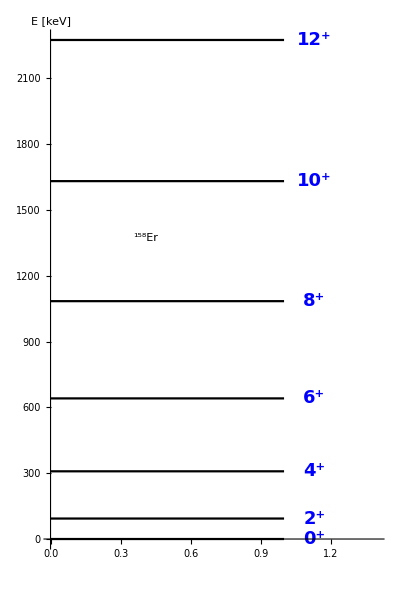

```mathematica
energies=Sort[{2274.3,1631.0,1084.006,640.849,308.576,93.3240,0.0}];
spins=Sort[Table[s,{s,0,2*Length[energies],2}]];
A="158";
element="Er";
energyLevels[spins_,levels_]:=Plot[energies,{x,0,1},Axes->{False,True},AspectRatio->1.5,AxesStyle->Directive[Black,Thick],PlotStyle->Black,PlotRange->{{0,1.4},Automatic},AxesLabel->{"","E [keV]"},LabelStyle->{20,Black,Bold,FontFamily->"Arial"},Epilog->{Table[Inset[Style[Superscript[spins[[i]],"+"],18,Blue,Bold,FontFamily->"Arial"],{1.13,levels[[i]]}],{i,1,Length[levels]}],Inset[Framed[Style[Row[{Superscript["",A],element}],Black,Bold,18]],Scaled[{0.3,0.6}]]}];
graf=energyLevels[spins,energies];
Show[graf]
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/rotational-bands-nuclei/Er158-Rotational-Bands.pdf",graf];
```